# Číslicové a analogové obvody Ukázkový test č.1

1) Zadefinujte funkci f takovou, že f(x)=sinh(x^2) a vytiskněte graf této funkce v argumentu  x=√(t+1) pro -1≤t≤1, tedy y=f(√(t+1)), (libovolně) popište osy a křivka nechť je silná a červená. [2 b]

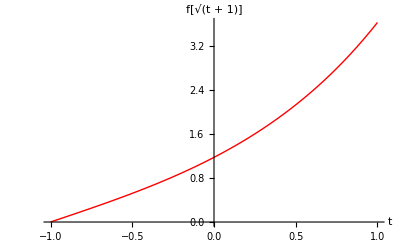

```mathematica
(*sem napiste reseni: *)
f[x_]:=Sinh[x^2]
Plot[f[√(t+1)],{t,-1,1}, AxesLabel->{"t","f[√(t + 1)]"},PlotStyle->{Thick, Red}]
```

2) Vyřešte soustavu rovnic. Dále pak dosaďte jen druhé řešení (hodnota x_2 je přibližně 1.57) do výrazu vyr.  Hodnotu výrazu vyr po dosazení zobrazte jako desetinné číslo na 10 desetinných míst. [2 b]

```mathematica
uloha2={1 Subscript[x, 2]^2+2 Subscript[x, 3]+Subscript[x, 1]==3,5 Subscript[x, 1]-3 Subscript[x, 2]+2 Subscript[x, 3]==-4,-21 Subscript[x, 1]+15 Subscript[x, 3]==3};
vyr=Subscript[x, 1]+Subscript[x, 2]^2+Subscript[x, 3]^2;

(*sem napiste reseni: *)
reseni2=Solve[uloha2]
dosazeno=vyr/.reseni2[[2]]
N[dosazeno,11]
```

{{x_1→(-857-5 √32109)/1014,x_2→1/78 (-57-√32109),x_3→(-997-7 √32109)/1014},{x_1→(-857+5 √32109)/1014,x_2→1/78 (-57+√32109),x_3→(-997+7 √32109)/1014}}

(-57+√32109)^2/6084+(-857+5 √32109)/1014+(-997+7 √32109)^2/1028196

2.556850199

3) Vyřešte soustavu diferenciálních rovnic pro soustavu počátečních podmínek, pro 0<t<40. Vytiskněte graf x1(t) a x2(t) a pomocí příkazu ParametricPlot také graf x2(x1). [3 b]

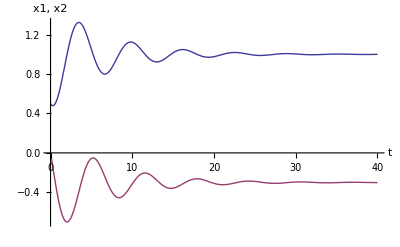

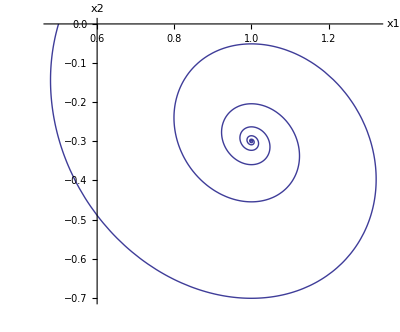

```mathematica
soustavaRovnic={x1'[t]+x2[t]==-3/10*x1[t],x1[t]-x2'[t]==1};
soustavaPodminek={x1[0]==1/2,x2[0]==0};

(*sem napiste reseni: *)
rovniceVsechny=Union[soustavaRovnic,soustavaPodminek];
neznameDif={x1[t],x2[t]};
tmax=40;
reseniDif=NDSolve[rovniceVsechny,neznameDif,{t,0,tmax}];
Plot[Evaluate[neznameDif/.reseniDif],{t,0,tmax},AxesLabel->{"t", "x1, x2"},PlotStyle->Thick,PlotRange->All]
ParametricPlot[Evaluate[neznameDif/.reseniDif],{t,0,tmax},AxesLabel->{"x1","x2"},PlotStyle->Thick,PlotRange->All]
```

4) Vyřešte soustavu 2 rovnic neznámých x a y s parametry t a u. Vyčíslete řešení pro hodnoty parametrů t = 1,5 a u = 2,3. Zobrazte graf závislosti neznámé x na hodnotách parametrů t a u pro -5≤t≤5 a 0≤u≤1, tedy graf x(t, u). Popište osy grafu. [3 b]

```mathematica
uloha4={2x+3u*y==5+Cos[t],4x-8y+Sin[2u+Pi/4]==3.2t};

(*sem napiste reseni: *)
reseni5=Solve[uloha4,{x,y}]
vycisleni=reseni5/.{t->1.5,u->2.3}
Print["Pro zadané hodnoty parametrů t a u mají neznámé hodnoty x=", x/.vycisleni[[1]]," a y=", y/.vycisleni[[1]],"."]
Plot3D[x/.reseni5,{t,-5,+5},{u,0,1}, PlotRange->All,AxesLabel->{"t","u","x"}]
```

{{x→2.5+0.5 Cos[t]+(1.5 u (-4. (-5.-1. Cos[t])+2. (-3.2 t+Sin[0.785398+2. u])))/(-16.-12. u),y→-(1. (-4. (-5.-1. Cos[t])+2. (-3.2 t+Sin[0.785398+2. u])))/(-16.-12. u)}}

{{x→1.81379,y→0.209153}}

Pro zadané hodnoty parametrů t a u mají neznámé hodnoty x=1.81379 a y=0.209153.

-Graphics3D-